```mathematica
Plot[{
        𝔼cLevtp1OcLevt[mPlot]
	,((R) β)^(1/ρ)
	,Γ
	}
	,{mPlot,mPlotMin,mPlotMax}
	,PlotRange->{{mPlotMin,mPlotMax+0.2},{yPlotMin,yPlotMax}}
	,AxesOrigin->{mPlotMin,yPlotMin}
    ,PlotStyle->{Black,Black,Black}
	,DisplayFunction->Identity
]
```

Plot::plln: Limiting value mPlotMin in {mPlot,mPlotMin,mPlotMax} is not a machine-sized real number.

Plot[{𝔼cLevtp1OcLevt[mPlot],(R β)^(1/ρ),Γ},{mPlot,mPlotMin,mPlotMax},PlotRange→{{mPlotMin,mPlotMax+0.2},{yPlotMin,yPlotMax}},AxesOrigin→{mPlotMin,yPlotMin},PlotStyle→{Black,Black,Black},DisplayFunction→Identity]

```mathematica
{𝔼aLevtp1OaLevt[1.5],𝔼mLevtp1OmLevt[1.5]}
```

{0.98852,1.72667}

```mathematica
κ'[mbg]
```

-0.362263

```mathematica
𝒶'[mbg]
```

0.739548

```mathematica
mbg = mt /. FindRoot[{𝔼aLevtp1OaLevt[mt] == 𝔼cLevtp1OcLevt[mt]},{mt,1,2}]
```

1.41402

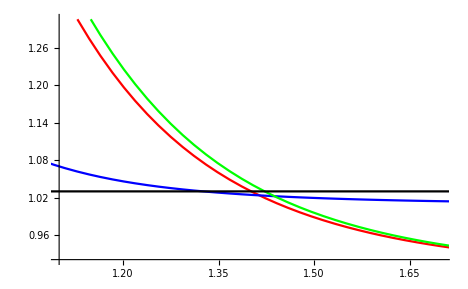

```mathematica
𝒶[𝓂_]:=𝓂-𝒸[𝓂];
𝔼aLevtp1OaLevt[mt_]                := 𝔼Fromat[Γtp1 𝒶[mtp1] &, 𝒶[mt]]/𝒶[mt]; 
𝔼cLevtp1OcLevt0[mt_]                := 𝔼Fromat[Γtp1 𝒸[mtp1] &, 𝒶[mt]]/𝒸[mt]; 
𝔼cLevtp1OcLevt1[mt_]                := 𝔼Fromat[Γ(Γtp1/Γ) (𝒶[mt]((R)/Γtp1)+(mtp1-btp1)) &, 𝒶[mt]]/𝒸[mt]; 
𝔼cLevtp1OcLevt1[mt_]                := 𝔼Fromat[Γtp1 (𝒸[mbg]+(mtp1-mbg)κ[mbg]+(1/2)κ'[mbg](mtp1-mbg)^2)&, 𝒶[mt]]/𝒸[mt]; 
𝔼aLevtp1OaLevt1[mt_]                := 𝔼Fromat[Γtp1 (𝒶[mbg]+(mtp1-mbg)𝒶'[mbg]+(1/2)𝒶''[mbg](mtp1-mbg)^2)&, 𝒶[mt]]/𝒶[mt]; 
(*𝔼aLevtp1OaLevt[mt_]                := 𝔼Fromat[Γtp1 𝒶[mtp1] &, 𝒶[mt]]/𝒶[mt]; 
𝔼aLevtp1OaLevt[mt_]                := 𝔼Fromat[Γtp1 𝒶[mtp1] &, 𝒶[mt]]/𝒶[mt]; 
𝔼mLevtp1OmLevt[mt_]                := 𝔼Fromat[Γtp1 mtp1 &, 𝒶[mt]]/mt; 
𝔼mLevtp1OmLevt0[mt_]                := 𝔼Fromat[Γ(Γtp1/Γ) (𝒶[mt]((R)/Γtp1)+(mtp1-btp1)) &, 𝒶[mt]]/mt; 
𝔼mLevtp1OmLevt1[mt_]                := 𝔼Fromat[𝒶[mt](R)+Γ &, 𝒶[mt]]/mt; 
𝔼aLevtp1OaLevt[mt_]                := 𝔼Fromat[Γtp1 𝒶[mtp1] &, 𝒶[mt]]/𝒶[mt]; 
𝔼mLevtp1OmLevt[mt_]                := 𝔼Fromat[Γtp1 mtp1 &, 𝒶[mt]]/mt; 
𝔼mLevtp1OmLevt0[mt_]                := 𝔼Fromat[Γ(Γtp1/Γ) (𝒶[mt]((R)/Γtp1)+(mtp1-btp1)) &, 𝒶[mt]]/mt; 
𝔼mLevtp1OmLevt1[mt_]                := 𝔼Fromat[𝒶[mt](R)+Γ &, 𝒶[mt]]/mt; *)
Del=0.1;
Plot[{
        𝔼aLevtp1OaLevt[mPlot]
,𝔼cLevtp1OcLevt[mPlot]
, 0.5(       𝔼aLevtp1OaLevt[mPlot+Del]+𝔼aLevtp1OaLevt[mPlot-Del])
(*
,𝔼cLevtp1OcLevt[mPlot]

,𝔼mLevtp1OmLevt1[mPlot]
,𝔼mLevtp1OmLevt[mPlot]
	,((R) β)^(1/ρ)*)
	,Γ
	}
	,{mPlot,mPlotMin,mPlotMax}
	,PlotRange->{{1.1,1.7},Automatic}
	,AxesOrigin->{1.1,Automatic}
    ,PlotStyle->{Red,Blue,Green,Black}
	,DisplayFunction->Identity
]
```

```mathematica
𝔼aLevtp1OaLevt[mbg]
```

1.02362

```mathematica
Del /. FindRoot[0.5(       𝔼aLevtp1OaLevt[mbg+Del]+𝔼aLevtp1OaLevt[mbg-Del])==Γ,{Del,0.01,0.4}]
```

0.0771972

```mathematica
Del /. FindRoot[0.5(       𝔼cLevtp1OcLevt[mbg+Del]+𝔼cLevtp1OcLevt[mbg-Del])==Γ,{Del,0.01,0.4}]
```

0.201817

```mathematica
Del /. FindRoot[0.5(       𝔼mLevtp1OmLevt[mbg+Del]+𝔼mLevtp1OmLevt[mbg-Del])==Γ,{Del,0.01,0.4}]
```

0.153706